## Généralités

```mathematica
(* matrice de transfert d'un site au suivant *)
M[tr_,tl_,e_]:={{e/tr,-tl/tr},{1,0}};
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
%//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* matrice de transfert de la 4-molécule *)
M1/.v->r v;
%.M1//Expand;
M2=%
```

{{-e^2/r-e^2 r-e^2/(r v^2)+e^4/(r v^2)+r v^2,e r+e/(r v^2)-e^3/(r v^2)},{-e/r-e/(r v^2)+e^3/(r v^2),1/(r v^2)-e^2/(r v^2)}}

```mathematica
(* couplages renormalisés *)
vv=(r v^2)/(e^2-1);
e1=e(1-r^-1 vv);
e2=e(1-r vv);
(* la 4-molécule correspond bien à une 2-molécule avec les couplages renormalisés *)
M[1,vv,e2].M[vv,1,e1];
%//Expand//Simplify;
%==Simplify[M2]
```

True

## Molécules isolées

#### Intro

```mathematica
(* matrice de transfert de la 2-molécule *)
M1=M[1,v,e].M[v,1,e];
M1//MatrixForm
```

(e^2/v-v | -e/v
e/v | -1/v)

```mathematica
(* hamiltonien dans la base atomique *)
h4={{0,1,0,0},{1,0,v,0},{0,v,0,1},{0,0,1,0}};
%//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | v | 0
0 | v | 0 | 1
0 | 0 | 1 | 0)

Dans le cas d’une molécule isolée on a des conditions aux limites nulles. Cela donne pour la fonction d’onde d’énergie E dont les coefficients sont les ψ_i dans la base atomique les conditions :
E ψ_0 = t_(0,1) ψ_1
E ψ_N= t_(N,N-1) ψ_(N-1) 
Dans la suite on suppose t_(0,1)=t_(N,N-1)=1. C’est de toute façon le cas pour nos molécules.
On peut grâce à la condition aux limites au bord gauche choisir (ψ_1, ψ_0) = (E, 1). Le vecteur propre ne sera alors pas normalisé, mais peu importe. 
Appelons M la matrice de transfert qui va d’un bord à l’autre du système, ie celle qui donne :
M (ψ_1, ψ_0) = (ψ_N, ψ_(N-1))
Après application de M sur (ψ_1, ψ_0), on obtient ψ_N comme un polynôme de degré N-1 en E. Grâce à la condition aux limites au bord droit on obtient une équation polynomiale de degré N à résoudre, qui nous donne les N énergies propres du système.

```mathematica
M1.{e ,1}//Expand;
spec4=Solve[e*%[[1]]==%[[2]],e]
(* les énergies obtenues sont bien celles de la 4-molécule *)
Eigenvalues[h4]
```

{{e→1/2 (-v-√(4+v^2))},{e→1/2 (v-√(4+v^2))},{e→1/2 (-v+√(4+v^2))},{e→1/2 (v+√(4+v^2))}}

{1/2 (-v-√(4+v^2)),1/2 (v-√(4+v^2)),1/2 (-v+√(4+v^2)),1/2 (v+√(4+v^2))}

La matrice de transfert nous donne aussi les vecteurs propres.

```mathematica
Block[
{i=4,vp},
vp={1,e ,(M1.{e ,1})[[2]],(M1.{e ,1})[[1]]}/.spec4[[i]];
Print[vp//Expand];
((e/.spec4[[i]])^-1*h4.vp)//FullSimplify//Expand
]
```

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

{1,v/2+(√(4+v^2))/2,v/2+(√(4+v^2))/2,1}

### Spectre

#### Avec une matrice de transfert

```mathematica
(* matrice de transfert de la 4-molécule *)
Clear[M];
M[v_]:={{e^2/v-v,-e/v},{e/v,-1/v}};
```

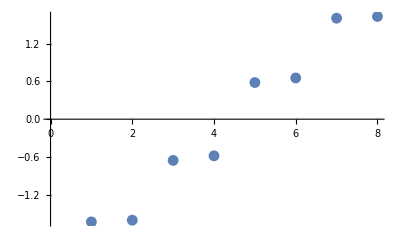

```mathematica
ClearAll[M,vv];
M[vv_]:={{e^2/vv-vv,-e/vv},{e/vv,-1/vv}};
ClearAll[r,v];
Block[{iter=1,v=1.,r=0.1,mf,transl,spec},
mf=Nest[{Expand[1/2#[[1]].(M[r^(#[[2]]) v]).#[[1]]],#[[2]]+1}&,{1/2 M[v],1},iter][[1]];
transl=mf.{e ,1};
spec=NSolve[e*transl[[1]]==transl[[2]],e];
ListPlot[e/.spec]
]
```

#### Diagonalisation directe

```mathematica
(* amplitude de saut entre les sites atomiques i et i+1 *)
Clear[t];
t[i_]:=Block[{k,tt},
k=IntegerExponent[i,2];
If[k==0,tt=1,tt=v r^(k-1)];
tt]
```

```mathematica
(* hamiltonien avec conditions aux bords nulles *)
Clear[h];
h[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+Transpose[ar]
]
```

Eigenvalues::arh: Because finding 2048 out of the 2048 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

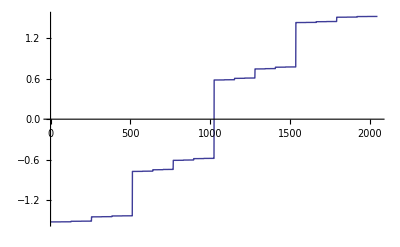

```mathematica
(* spectre *)
Block[{v=.8,r=0.3,vp},
vp=Sort[Eigenvalues[h[11]]];
ListPlot[vp,Joined->True]
]
```

Eigensystem::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

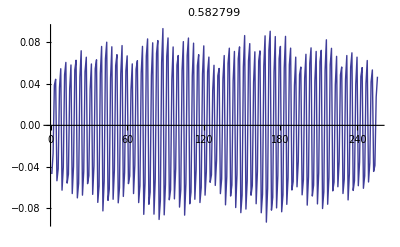

```mathematica
(* vecteurs propres *)
Block[{v=.8,r=0.3,val,vp,i=256},
{val,vp}=Eigensystem[h[8]];
ListPlot[vp[[i]],Joined->True,PlotLabel->val[[i]]]
]
```

```mathematica
(* hamiltonien avec conditions aux bords périodiques *)
Clear[hp];
hp[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+Transpose[ar]
]
hp[2]//MatrixForm
```

(0 | 1 | 0 | v
1 | 0 | v | 0
0 | v | 0 | 1
v | 0 | 1 | 0)

```mathematica
(* hamiltonien avec conditions aux bords antipériodiques *)
Clear[ha];
ha[n_]:=Block[{tbl,ar},
tbl=Table[{i,i+1}->t[i],{i,1,2^n-1}];
(* clp *)
tbl=Join[tbl,{{1,2^n}->-t[2^(n-1)]}];
ar=SparseArray[tbl,{2^n,2^n}];
ar+Transpose[ar]
]
ha[2]//MatrixForm
```

(0 | 1 | 0 | -v
1 | 0 | v | 0
0 | v | 0 | 1
-v | 0 | 1 | 0)

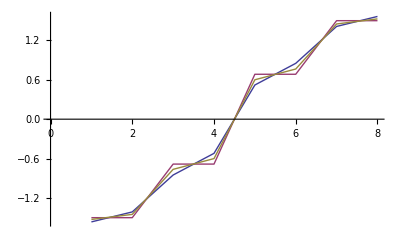

```mathematica
(* spectre *)
Block[{v=.8,r=0.3,vpp,vpa,vpn,i=3},
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
vpn=Sort[Eigenvalues[h[i]]];
ListPlot[{vpp,vpa,vpn},Joined->True]
]
```

Eigenvalues::arh: Because finding 4096 out of the 4096 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

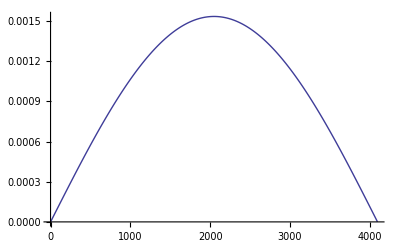

{τ→-1.20478}

1.2

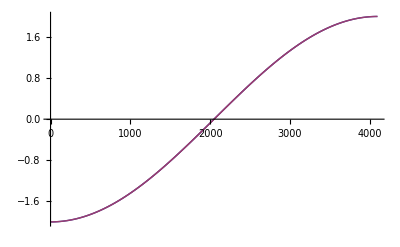

```mathematica
(* box counting *)
Block[{v=1.,r=1.,vpp,vpa,bandlist,i=12,gam,chi,meanband},
vpp=Sort[Eigenvalues[hp[i]]];
vpa=Sort[Eigenvalues[ha[i]]];
(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bandlist=MapThread[Abs[#1-#2]&,{vpa,vpp}];
(* limite singulière quand r->1, r<1 !! *)
Print[ListPlot[bandlist,Joined->True]];
(* calcul de Γ *)
gam=2^-q Plus@@((bandlist)^-τ);
meanband=Mean[bandlist];
chi=Plus@@((bandlist)^q);
(* Subscript[D, 0] *)
Print[FindRoot[(gam/.q->0)-1,{τ,-1}]];
Print[Log[chi/.q->0]/( -Log[meanband])];
ListPlot[{vpp,vpa},Joined->True]
]
```